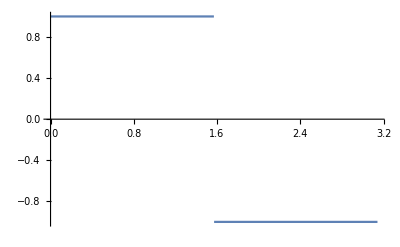

```mathematica
step[x_] := Piecewise[ {{1,x<Pi/2},{-1,x>=Pi/2}} ];
Plot[step[x],{x,0,Pi}]
```

12

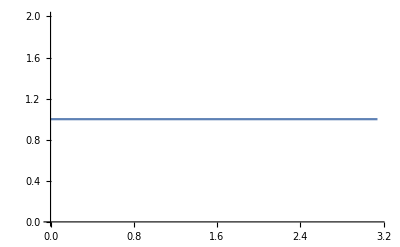
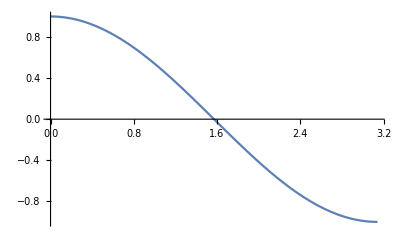
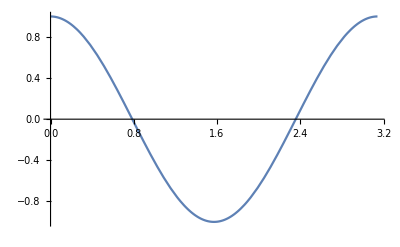
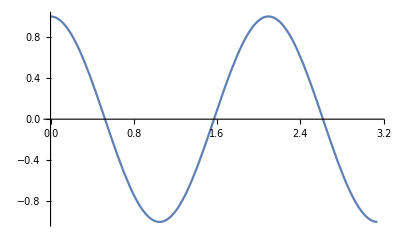
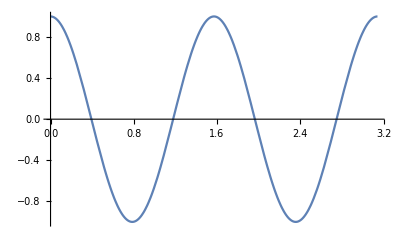
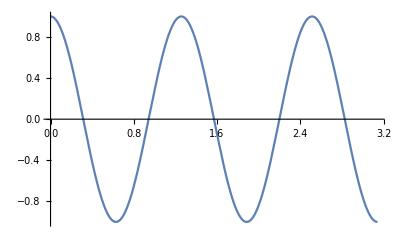
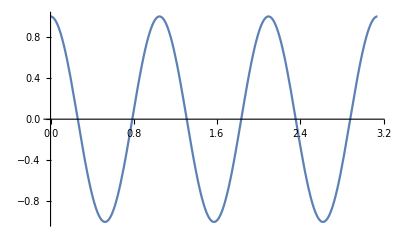
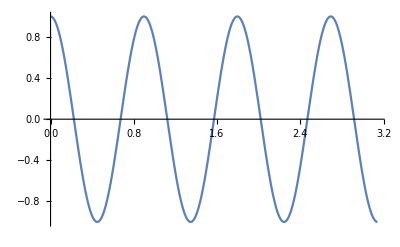

```mathematica
numTerms = 12
v = Table[ Cos[ n x], {n,0,numTerms-1}];
Table[ Plot[v[[i]],{x,0,Pi}], {i,1,numTerms}]
```

```mathematica
innerProduct[f_,g_] := Integrate[ f*g,{x,0,Pi}];
Table[ innerProduct[v[[i]],v[[j]]], {i,1,10},{j,1,10}] // MatrixForm
```

(π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | π/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | π/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | π/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | π/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | π/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | π/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | π/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π/2)

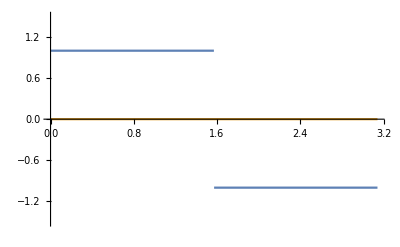
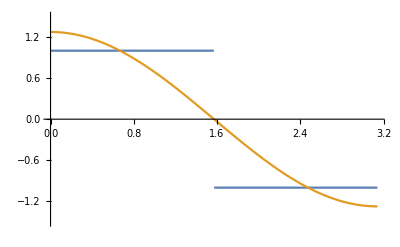
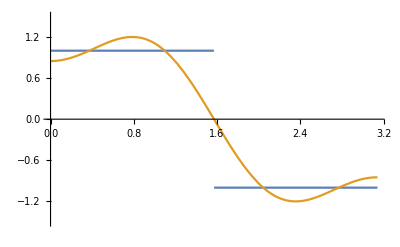
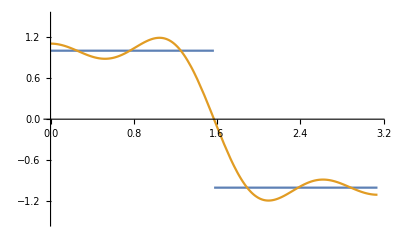
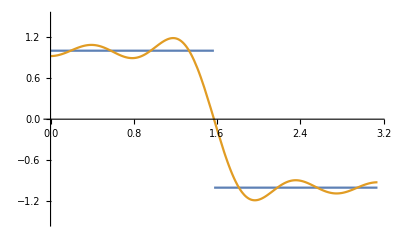
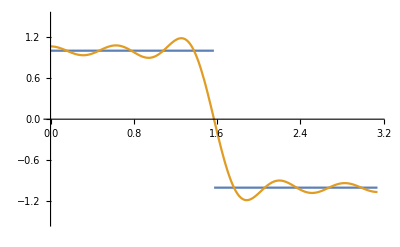
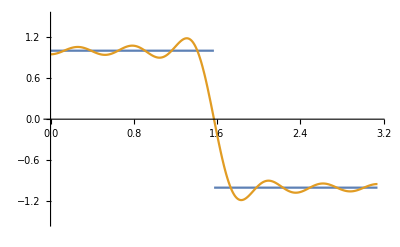
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
project[f_,g_] := innerProduct [f,g] / innerProduct[g,g] * g;
terms =Table[project[step[x],v[[i]]],{i,1,numTerms}];
partialSums = Table[ Sum[terms[[j]],{j,1,i}],{i,1,numTerms}];
Table[ Plot[{step[x],partialSums[[i]]},{x,0,Pi},PlotRange->{-1.5,1.5}],{i,1,numTerms}]
```

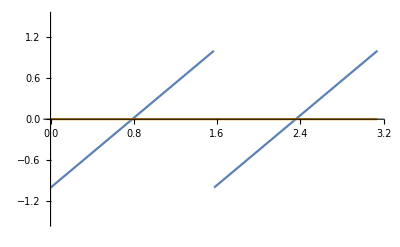
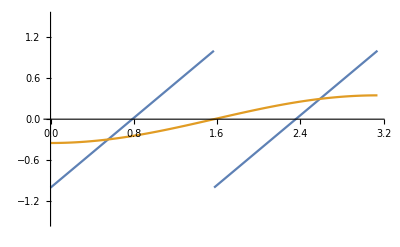
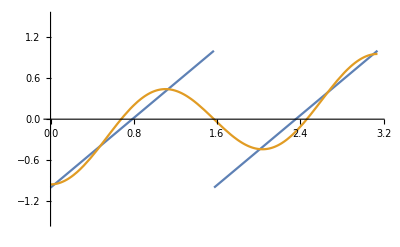
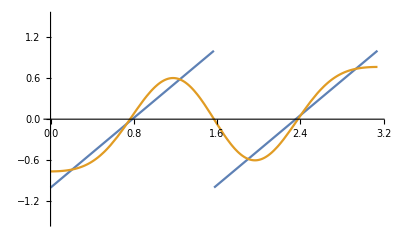
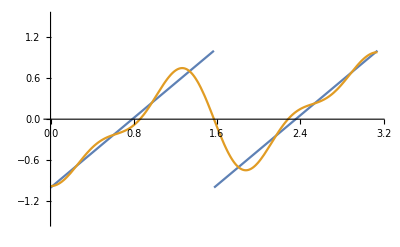
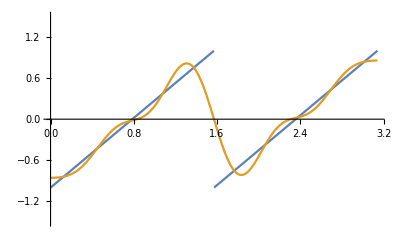
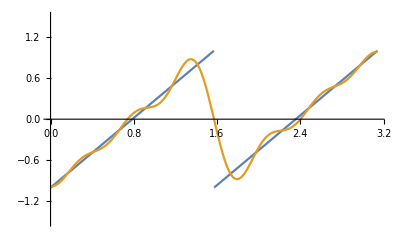
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sawtooth[x_] := -1+2*FractionalPart[2/Pi*x];
terms =Table[project[sawtooth[x],v[[i]]],{i,1,numTerms}];
partialSums = Table[ Sum[terms[[j]],{j,1,i}],{i,1,numTerms}];
Table[ Plot[{sawtooth[x],partialSums[[i]]},{x,0,Pi},PlotRange->{-1.5,1.5}],{i,1,numTerms}]
```

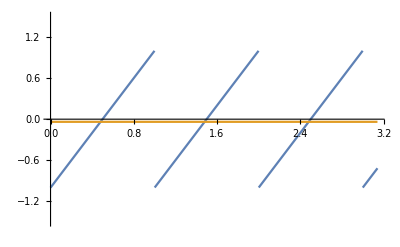
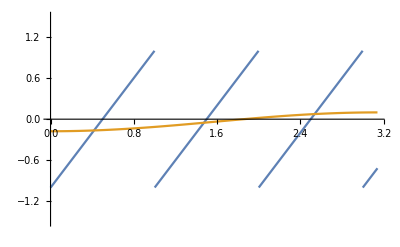
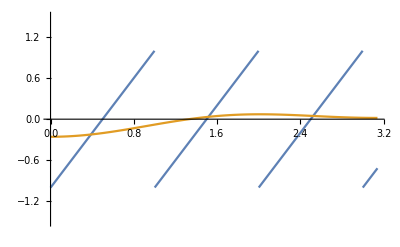
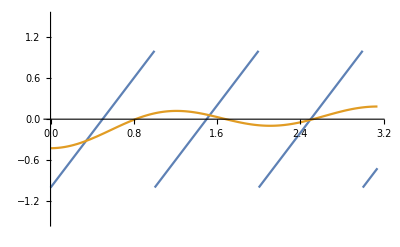
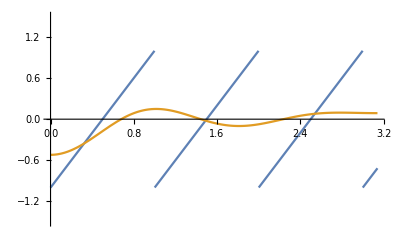
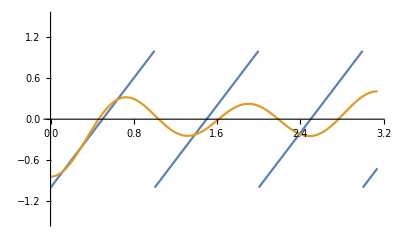
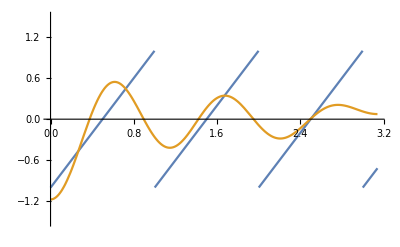
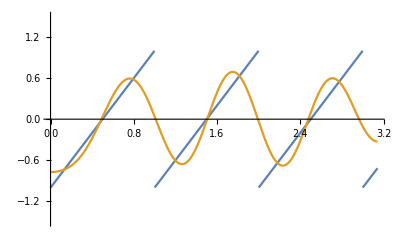

```mathematica
fastersawtooth[x_] := -1+2*FractionalPart[x];
terms =Table[project[fastersawtooth[x],v[[i]]],{i,1,numTerms}];
partialSums = Table[ Sum[terms[[j]],{j,1,i}],{i,1,numTerms}];
Table[ Plot[{fastersawtooth[x],partialSums[[i]]},{x,0,Pi},PlotRange->{-1.5,1.5}],{i,1,numTerms}]
```